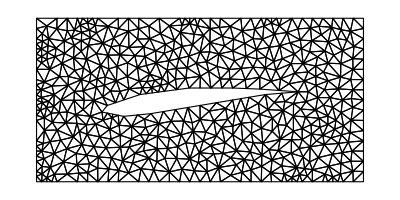

```mathematica
(* Start of given code *)
wing = Polygon[{{-18,-2.2},{-14,-3},{-9,-2.5},{0,-1},{12,1},{18,1.5},{11,2},{6,2.2},{-2,2.2},{-11,1},{-17,-1},{-18,-2.2}}];
rectangle = Rectangle[{-30,-15},{30,15}];
reg = RegionDifference[rectangle,wing];
Needs["NDSolve`FEM`"]
mesh=ToElementMesh[DiscretizeRegion[reg],MaxCellMeasure->3,"MeshOrder"-> 1];
mesh["Wireframe"]
(*Remove semicolon for more detailed mesh*)
Show[mesh["Wireframe"["MeshElementIDStyle"->Red]],mesh["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Blue]]];
nodes = mesh["Coordinates"];
elements = mesh["MeshElements"][[1,1]];
boundary =Flatten[mesh["BoundaryElements"]⟦1,1⟧];
boundary=DeleteDuplicates[boundary];
Subscript[Γ, els]=N[{{-18,-2.2},{-14,-3},{-9,-2.5},{0,-1},{12,1},{18,1.5},{11,2},{6,2.2},{-2,2.2},{-11,1},{-17,-1},{-18,-2.2}}];
upp = Cases[nodes⟦boundary⟧,{_,y_}/;y== 15.];
low = Cases[nodes⟦boundary⟧,{_,y_}/;y== -15.];
For[i=1,i≤ Length[low],i++,
AppendTo[Subscript[Γ, els],low⟦i⟧]; 
];
For[i=1,i≤ Length[upp],i++,
AppendTo[Subscript[Γ, els],upp⟦i⟧]; 
];
Subscript[Γ, in]=Cases[nodes⟦boundary⟧,{x_,_}/;x== -30.];
Subscript[Γ, out]=Cases[nodes⟦boundary⟧,{x_,_}/;x== 30.];inElems=Table[{Position[nodes,Sort[Subscript[Γ, in]]⟦i⟧]⟦1,1⟧,Position[nodes,Sort[Subscript[Γ, in]]⟦i+1⟧]⟦1,1⟧},{i,1,Length[Subscript[Γ, in]]-1}];
outNodes = Table[Position[nodes, Subscript[Γ, out]⟦i⟧]⟦1,1⟧,{i,1,Length[Subscript[Γ, out]]}];
(* End of given code *)
```

```mathematica
(* Standard basis functions, i.e. shape functions *)
Subscript[ψ, 0][{ξ_,η_}]:=1-ξ-η
Subscript[ψ, 1][{ξ_,η_}]:=ξ
Subscript[ψ, 2][{ξ_,η_}]:=η
gradψ=Transpose@Grad[{Subscript[ψ, 0][{ξ,η}],Subscript[ψ, 1][{ξ,η}],Subscript[ψ, 2][{ξ,η}]},{ξ,η}];
gradψT=Transpose@gradψ;

(* The Jacobian and Jacobian inverse *)
(* Here we utilise the fact that R^2 vectors are represented as lists and we can directly get their "transpose" by using the list *)
J[elementNodes_]:={
elementNodes⟦2⟧-elementNodes⟦1⟧,
elementNodes⟦3⟧-elementNodes⟦1⟧}
B[elementNodes_]:={
{elementNodes⟦3,2⟧-elementNodes⟦1,2⟧,elementNodes⟦1,2⟧-elementNodes⟦2,2⟧},
{elementNodes⟦1,1⟧-elementNodes⟦3,1⟧,elementNodes⟦2,1⟧-elementNodes⟦1,1⟧}}

(* The local stiffness matrix *)
(* Formally, we would have to do something like this 
localStiffness[nodes_, element_]:=
1/(Det@J[nodes,element])NIntegrate[gradψT.(Transpose@B[nodes,element]).B[nodes,element].gradψ,{ξ,0,1},{η,0,1-ξ}]*)
(* However the integrand is constant so we just need to multiply it by the area of the standard triangle, which is 1/2 *)
localStiffness[elementNodes_]:=
0.5/(Det@J[elementNodes])gradψT.Transpose@B[elementNodes].B[elementNodes].gradψ

FEMMatrix[nodes_,elements_,localFunction_,nullNodes_]:=Module[{
globalMatrix = ConstantArray[0,{Length@nodes,Length@nodes}], element, quality},
For[k=1,k≤Length@elements,k++,
element = elements⟦k⟧;
quality=localFunction@nodes⟦element⟧;
For[i=1,i≤3,i++,
For[j=1,j≤3,j++,
globalMatrix⟦element⟦i⟧,element⟦j⟧⟧+=quality⟦i, j⟧;
];
];
];

(* We should now take into account that some of the coefficients will have to be 0 to ensure the boundary condition of u=0 *)
For[i=1,i≤Length@nullNodes,i++,
For[j=1,j≤Length@nodes,j++,
globalMatrix⟦j,nullNodes⟦i⟧⟧=0;
globalMatrix⟦nullNodes⟦i⟧,j⟧=0;
];
globalMatrix⟦nullNodes⟦i⟧,nullNodes⟦i⟧⟧=1;
];

globalMatrix
]

(* The function that assebles the global stiffness matrix *)
stiffnessMatrix[nodes_,elements_,nullNodes_]:=FEMMatrix[nodes,elements,localStiffness,nullNodes]

(* The local inner load array *)
localInnerLoad[f_,elementNodes_]:=Module[
{jacobian = J@elementNodes,
origin=elementNodes⟦1⟧},
1/6 Det[jacobian]Table[
Subscript[ψ, s][{0.5,0}]f[jacobian.{0.5,0}+origin]+
Subscript[ψ, s][{0.5,0.5}]f[jacobian.{0.5,0.5}+origin]+
Subscript[ψ, s][{0,0.5}]f[jacobian.{0,0.5}+origin],{s,0,2}]
]

(* The local boundary load array *)
localBoundaryLoad[boundaryElementNodes_]:=(
ConstantArray[
0.5Norm[boundaryElementNodes⟦1⟧-boundaryElementNodes⟦2⟧],
2]
)

(* boundaryElements holds only the boundary elements that don't evaluate to 0 *)
loadVector[nodes_,elements_,boundaryElements_,localInnerLoadFunction_,localBoundaryLoadFunction_,nullNodes_]:=Module[{
globalVector=ConstantArray[0,Length@nodes],element},

(* The load from double integrals *)
For[k=1,k≤Length@elements,k++,
element = elements⟦k⟧;
globalVector⟦element⟧+=localInnerLoadFunction[nodes⟦element⟧];
];

(* The load from boundary integrals *)
For[k=1,k≤Length@boundaryElements,k++,
globalVector⟦boundaryElements⟦k⟧⟧+=localBoundaryLoadFunction@nodes⟦boundaryElements⟦k⟧⟧;
];

(* Where u=0 we should have loadVector=0 *)
globalVector⟦nullNodes⟧=0;

globalVector
]
```

```mathematica
(* Solve the FEM system *)
particularInnerLoad[elementNodes_]:=localInnerLoad[0&,elementNodes]
Subscript[M, 1]=stiffnessMatrix[nodes,elements,outNodes];
b=loadVector[nodes,elements,inElems,particularInnerLoad,localBoundaryLoad,outNodes];
q=LinearSolve[Subscript[M, 1],b];
Φ=Interpolation[Thread[{nodes,q}],InterpolationOrder->1];
```

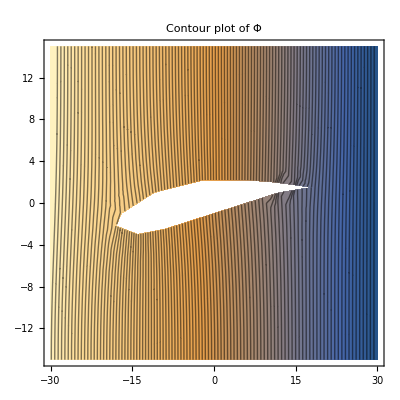

```mathematica
(* Plot potential Φ *)
ContourPlot[Φ[x,y],{x,y}∈RegionDifference[rectangle,wing],PlotLabel->"Contour plot of Φ",Contours->100]
```

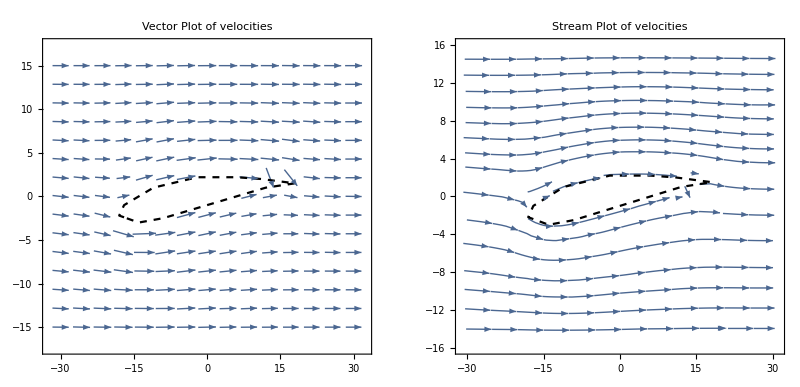

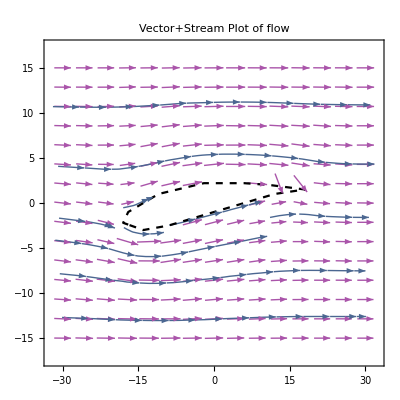

```mathematica
(* Plot flow -∇Φ *)
(* We should take -∇Φ as that makes sense in modelling the wing - air will flow from the front *)
velocityField=-∇_{x,y} Φ[x,y];
GraphicsGrid[
{{Show[
{VectorPlot[velocityField,{x,y}∈reg,PlotLabel->"Vector Plot of velocities"],
RegionPlot[wing,PlotStyle->Transparent,BoundaryStyle->{Black,Dashed}]}
],
Show[
{StreamPlot[velocityField,{x,y}∈reg,PlotLabel->"Stream Plot of velocities"],
RegionPlot[wing,PlotStyle->Transparent,BoundaryStyle->{Black,Dashed}]}
]
}}
]
Show[
{VectorPlot[velocityField,{x,y}∈reg,StreamPoints->Coarse,VectorStyle->Lighter@Purple,PlotLabel->"Vector+Stream Plot of flow"],
RegionPlot[wing,PlotStyle->Transparent,BoundaryStyle->{Black,Dashed}]}
]
```